# BASICS OF GRAPH THEORY

Peter Cullen Burbery

Abstract

## GRAPHS AND THEIR PARTS

We write a graph G as G = VUE, where V is a finite set and E is a finite multiset. The elements of V are called vertices while the elements
of E are called edges.

We will make a graph:

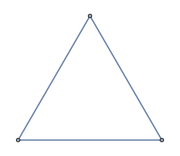

```mathematica
G=CompleteGraph[3,ImageSize->Small]
```

Edges are unordered pairs of not necessarily distinct vertices from V. We call V =: V(G) the vertex set of G, while
E =: E(G) is called the edge set of G.

```mathematica
V=VertexList[G]
```

{1,2,3}

```mathematica
EE=EdgeList[G]
```

{1<->2,1<->3,2<->3}

Vertices joined by an edge are called adjacent. They are also called the ends of the edge.

```mathematica
AdjacencyList[G,1]
```

{2,3}

An edge is said to be incident to its ends.

```mathematica
IncidenceList[G,1]
```

{1<->2,1<->3}

If e E E(G) is joining x and y, then we may denote e as xy. A loop
of G is an edge of the form vv, v E V(G).

```mathematica
DeBruijnGraph[2,3]
```

-Graphics-

Cartesian graph product:

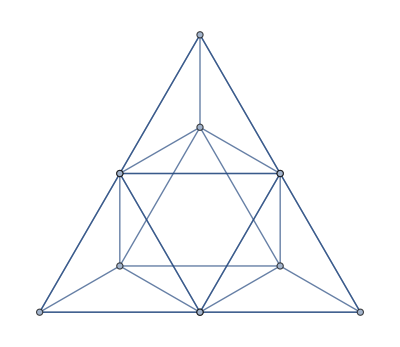

```mathematica
GraphProduct[CompleteGraph[3],CompleteGraph[4]]
```

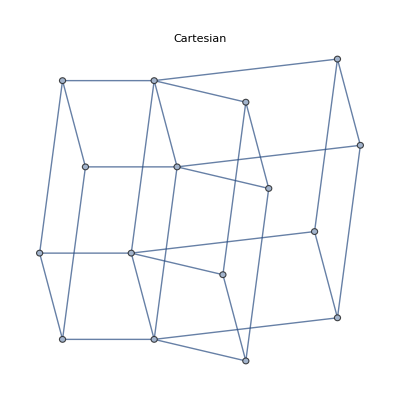
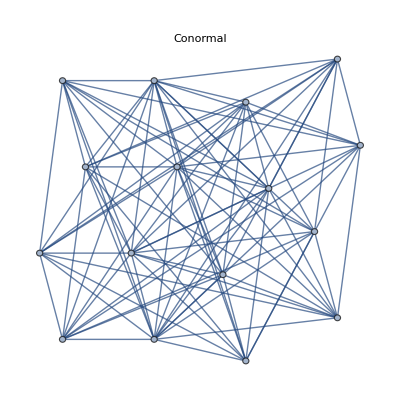
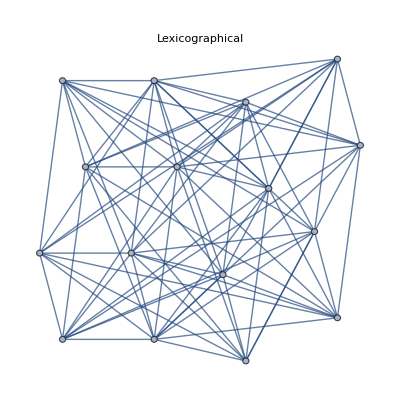
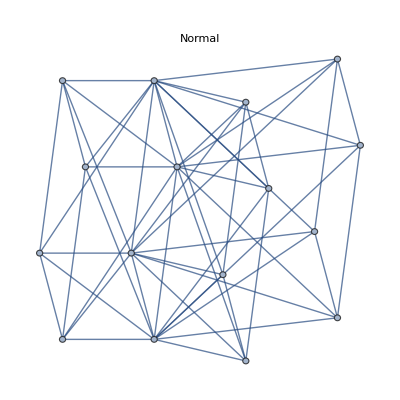
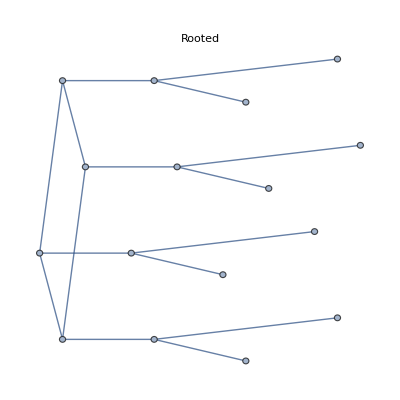
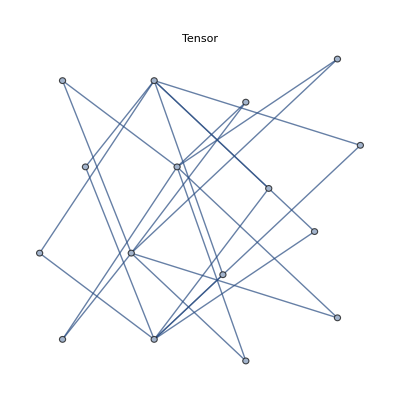

```mathematica
Table[GraphProduct[-Graphics-,-Graphics-,op,],{op,}]
```

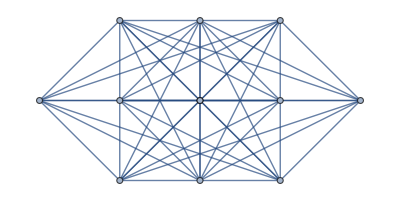

```mathematica
GraphProduct[CycleGraph[4],StarGraph[3],"Conormal"]
```

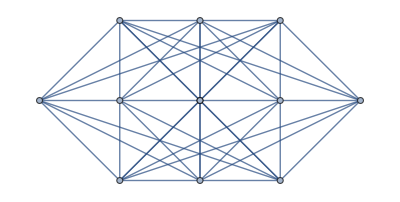

```mathematica
GraphProduct[CycleGraph[4],StarGraph[3],"Lexicographical"]
```

Likewise, a digraph D is the union of a finite vertex set V and a
finite multiset A, called arc set, which consists of ordered pairs of vertices, called arcs. The vertices joined by an arc a = (u, v) are also said
to be adjacent, with u being the tail of a and v being the head of the arc.

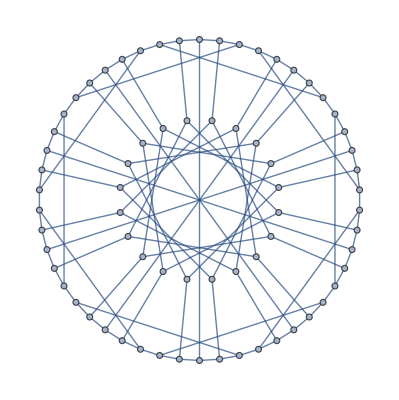

```mathematica
GraphData[First[GraphData["Cage"]]]
```

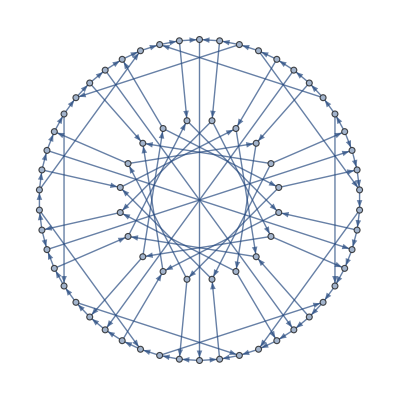

```mathematica
DirectedGraph[GraphData[First[GraphData["Cage"]]],"Acyclic"]
```

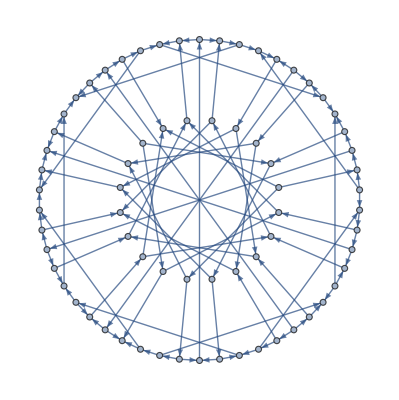

```mathematica
DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]
```

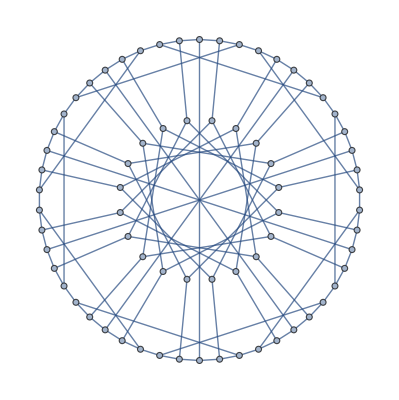

```mathematica
UndirectedGraph[DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]]
```

```mathematica
VertexCount[UndirectedGraph[DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]]]
```

70

```mathematica
VertexDegree[GraphData[First[GraphData["Cage"]]],6]
```

3

```mathematica
OddQ@VertexDegree[GraphData[First[GraphData["Cage"]]],6]
```

True

```mathematica
EvenQ@VertexDegree[GraphData[First[GraphData["Cage"]]],6]
```

False

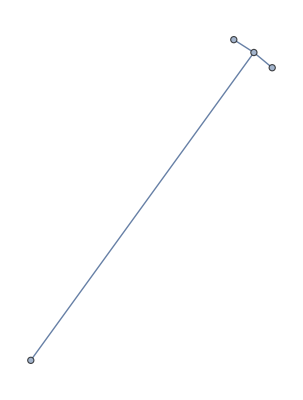

```mathematica
NeighborhoodGraph[GraphData[First[GraphData["Cage"]]],6]
```

```mathematica
IncidenceList[GraphData[First[GraphData["Cage"]]],6]
```

{5<->6,6<->7,6<->41}

```mathematica
Max@VertexDegree[GraphData[First[GraphData["Cage"]]]]
```

3

```mathematica
Min@VertexDegree[GraphData[First[GraphData["Cage"]]]]
```

3

```mathematica
VertexCount[GraphData[First[GraphData["Cage"]]]]
```

70

```mathematica
EdgeCount[GraphData[First[GraphData["Cage"]]]]
```

105

```mathematica
VertexInDegree[DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]]
```

{1,2,2,1,2,1,2,1,2,1,1,1,2,2,1,2,3,2,1,2,1,2,1,1,2,1,1,2,3,2,1,1,1,2,1,0,1,2,1,3,2,1,1,1,2,1,0,1,1,2,1,2,2,3,1,1,2,2,1,2,3,0,2,1,2,2,1,2,0,2}

```mathematica
VertexOutDegree[DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]]
```

{1,3,2,2,1,2,1,2,0,2,2,2,0,1,3,0,2,1,0,3,0,3,1,1,0,2,1,3,1,1,3,2,0,2,1,2,1,2,1,0,2,3,0,3,2,1,2,0,1,2,2,2,0,1,2,2,0,2,2,2,1,1,2,2,2,1,2,2,1,3}

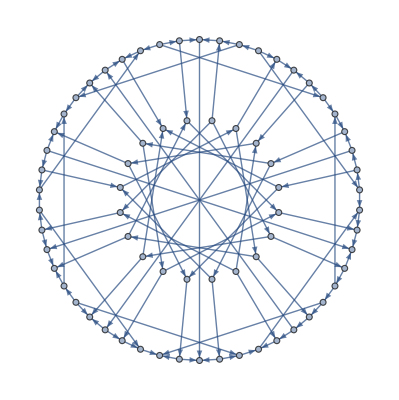

```mathematica
graph=DirectedGraph[GraphData[First[GraphData["Cage"]]],"Random"]
```

```mathematica
VertexList[graph,v_/;VertexInDegree[graph,v]==0]
```

{8,11,19,25,33,43}

```mathematica
VertexList[graph,v_/;VertexOutDegree[graph,v]==0]
```

{14,26,29,36,38,42,45,52}

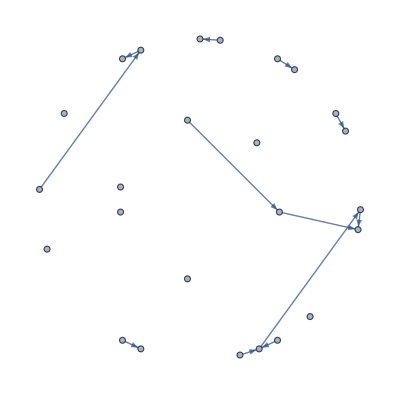

```mathematica
Subgraph[graph,VertexList[graph,v_/;VertexOutDegree[graph,v]==1]]
```

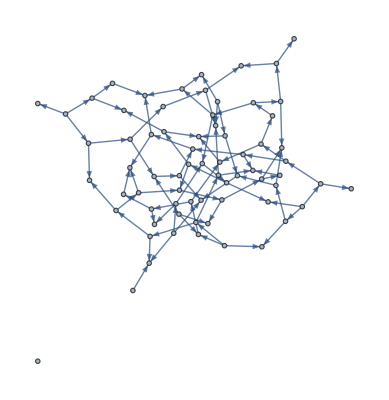

```mathematica
GraphDifference[graph,Subgraph[graph,VertexList[graph,v_/;VertexOutDegree[graph,v]==1]]]
```

```mathematica
GraphComplement[GraphDifference[graph,Subgraph[graph,VertexList[graph,v_/;VertexOutDegree[graph,v]==1]]]]
```

-Graphics-

```mathematica
FindVertexCut[graph]
```

{5,17,19}

```mathematica
FindEdgeCut[GraphData["PappusGraph"]]
```

{3<->18,15<->18,17<->18}

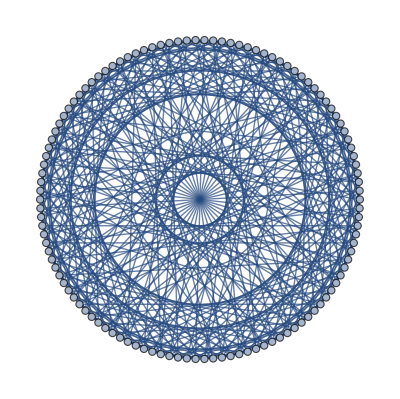

```mathematica
graph=GraphData[{"Cage",{8,6}}]
```

```mathematica
ConnectedComponents[graph]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114}}

```mathematica
WeaklyConnectedComponents[graph]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114}}

```mathematica
KCoreComponents[graph,2]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114}}

XXXX: